# Rania 2/11/2025 PS7

Section 18 Problems

3453.71 mi

1.35109

14387. km

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

6.64488

```mathematica
(**18.1 Find the distance from New York to London.**)
GeoDistance[,]

(**18.2 Divide the distance from New York to London by the distance from New York to San Francisco.**)
GeoDistance[,]/GeoDistance[,]

(**18.3 Find the distance from Sydney to Moscow in kilometers.**)
UnitConvert[GeoDistance[Entity["City",{"Sydney","NewSouthWales","Australia"}],],Quantity[, "Kilometers"]]

(**18.4 Generate a map of the United States.**)
GeoGraphics[]

(**18.5 Plot on a map Brazil,Russia,India,and China.**)
GeoListPlot[{,,,}]
(*indicate with {}*)

(**18.6 Plot on a map the path from New York City to Beijing.**)
GeoGraphics[GeoPath[{,}]]
(*indicate with {}*)

(**18.7 Plot a disk centered on the Great Pyramid,with radius 10 miles.**)
GeoGraphics[GeoDisk[Entity["Building","GreatPyramidOfGiza::jbm66"],Quantity[10, "Miles"]]]

(**18.8 Plot a disk centered on New York with a radius large enough to just reach San Francisco.**)
GeoGraphics[GeoDisk[,GeoDistance[,]]]

(**18.9 Make a satellite image of 0.4 miles around the Pentagon.**)
GeoImage[GeoDisk[,Quantity[0.4, "Miles"]]]

(**18.10 Find the nearest 5 countries to the North Pole (GeoPosition["NorthPole"]).**)
GeoNearest["Country",GeoPosition["NorthPole"],5]

(**18.11 Find the flags of the 3 countries nearest to latitude 45°,longitude 0°.**)
EntityValue[Take[GeoNearest["Country",GeoPosition[{45,0}],3]],"Flag"]

(**18.12 Plot the 25 volcanoes closest to Rome.**)
GeoListPlot[GeoNearest["Volcano",GeoPosition[Entity["City",{"Rome","Lazio","Italy"}]],25]]

(**18.13 Find the difference in latitude between New York and Los Angeles.**)
Part[Part[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]],1]- Part[GeoPosition[],1],1]
(*There must be a simpler way but the latitude is not a key and I didn't know what method he wanted me to do*)
```

Section 19 Problems

45697. days

Saturday

Thu 29 Apr 1751 01:24:15GMT-7

Tue 11 Feb 2025 13:54:15GMT+5.5

-10.8076 h

-Graphics-

{0.981443,0.998399,0.994506,0.971049,0.929957,0.87353,0.804225,0.7245,0.636771,0.543459,0.44712}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-4.54772 h

55.6014 yr

42.8 °F

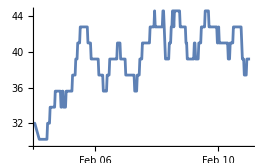

23.1 _Δ^◦F

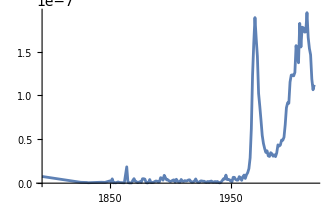

20759628 people

```mathematica
(**19.1 Compute how many days have elapsed since January 1,1900.**)
Now - DateObject[{1900,1,1},"Day"]

(**19.2 Compute what day of the week January 1,2000 was.**)
DayName[]

(**19.3 Find the date a hundred thousand days ago.**)
Now-

(**19.4 Find the local time in Delhi.**)
LocalTime[]

(**19.5 Find the length of daylight today by subtracting today’s sunrise from today’s sunset.**)
Sunrise[Today]-Sunset[Today]

(**19.6 Generate an icon for the current phase of the moon.**)
MoonPhase[Today,"Icon"]

(**19.7 Make a list of the numerical phase of the moon for each of the next 10 days.**)
Table[MoonPhase[n],{n,DateRange[Today,Today + Quantity[10, "Days"]]}]

(**19.8 Generate a list of icons for the moon phases from tomorrow until 10 days from now.**)
Table[MoonPhase[n,"Icon"],{n,DateRange[Today,Today + Quantity[10, "Days"]]}]

(**19.9 Compute the time today between sunrise in London and in New York City.**)
Sunrise[,Today]- Sunrise[,Today]

(**19.10 Find the number of years from the Apollo 11 moon landing until now.**)
UnitConvert[Now - DateObject[Entity["MannedSpaceMission","Apollo11"][EntityProperty["MannedSpaceMission","LunarLandingDate"]]],]

(**19.11 Find the air temperature at the Eiffel Tower at noon yesterday.**)
AirTemperatureData[,DateObject[{2025,2,10,12,0,0},"Instant","Gregorian",-7.]]

(**19.12 Plot the temperature at the Eiffel Tower over the past week.**)
ListLinePlot[AirTemperatureData[,{,Now}]]

(**19.13 Find the difference in air temperatures between Los Angeles and New York City now.**)
AirTemperatureData[, Now]-AirTemperatureData[, Now]

(**19.14 Plot the historical frequency of the word “groovy”.**)
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]

(**19.15 Find the difference in population of the UK between 2000 and 1900.**)
[Dated["Population",2000]]-[Dated["Population",1900]]
```